```mathematica
(*Mn^2 Subscript[ϕ, n](x) = ((Subscript[m, 1]^2-1)/x+(Subscript[m, 2]^2-1)/(1-x))Subscript[ϕ, n](x)-β^2(∫_0)^1 dy Subscript[ϕ, n](y) PV/(y-x)^2*)
```

```mathematica
ParallelEvaluate[Off[General::stop];];
```

```mathematica
Nx=30;
```

```mathematica
(*ϕ[n_][x_]:=√(α/(√π 2^n n!)) HermiteH[n,α x] E^(1/2 (-α^2) x^2)*)
ϕ[n_][x_]:=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
μsquare[n_]:=π^2(n-1);
```

```mathematica
α=0.5;m1=3.2;m2=3.2;β=0.137;λ=10^-6;
```

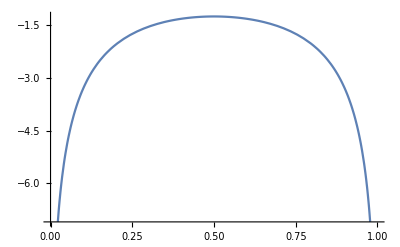

```mathematica
n=1;
Plot[-(NIntegrate[(ϕ[n][y])/(x-y)^2,{y,0,x-λ}]+NIntegrate[(ϕ[n][y])/(x-y)^2,{y,x+λ,1}])+2(ϕ[n][x])/λ-μsquare[n]ϕ[n][x],{x,0,1}]
Clear[n];
```

```mathematica
H1[m_,n_][x_?NumberQ]:=(m1/x+m2/(1-x))ϕ[m][x]ϕ[n][x];H2[m_,n_][x_?NumberQ]:=β^2/2 NIntegrate[Boole[(y>x+λ||y<x-λ)]((ϕ[n][x]-ϕ[n][y])(ϕ[m][x]-ϕ[m][y]))/(x-y)^2,{y,0,1}];
```

```mathematica
(*Use principal value P(∫_a)^b ⅆy (f(y))/(x-y)^2=(∫_a)^(x-λ)ⅆy (f(y))/(x-y)^2+(∫_(x+λ))^b ⅆy (f(y))/(x-y)^2-2/λ f(x)*)
```

```mathematica
Block[{i=1,j=2},NIntegrate[H1[i,j][x]-H2[i,j][x]+β^2 ϕ[i][x](ϕ[j][x])/λ,{x,0,1}]]
```

3218.36

```mathematica
HMat=ParallelTable[(*Print[{i,j}];*)NIntegrate[H1[i,j][x]-H2[i,j][x]+β^2 ϕ[i][x](ϕ[j][x])/λ,{x,0,1}],{i,1,Nx},{j,1,Nx}];
{vals,vecs}=Reverse[Eigensystem[%],2];
vals
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.638656}. NIntegrate obtained 2.16716×10^-13 and 1.27311×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 2.40696×10^-13 and 1.71589×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.505844}. NIntegrate obtained -4.61853×10^-14 and 1.31587×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 2.84217×10^-14 and 9.79809×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained -7.88702×10^-13 and 1.38895×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 1.13687×10^-13 and 1.64904×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.84928×10^-6}. NIntegrate obtained -1.48281×10^-13 and 1.77599×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 9.30811×10^-13 and 1.67148×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 3.41061×10^-13 and 1.13389×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9991913189932437725816749551910334048443473875522613525390625}. NIntegrate obtained -2.27374×10^-13 and 2.82935×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 6.6791×10^-13 and 2.4341×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained -2.84217×10^-13 and 3.05507×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 4.54747×10^-13 and 4.16232×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 1.00897×10^-12 and 3.29975×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 3.76588×10^-13 and 1.96171×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9991913189932437725816749551910334048443473875522613525390625}. NIntegrate obtained -7.95808×10^-13 and 5.73232×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.748031}. NIntegrate obtained -1.42109×10^-14 and 8.93424×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.863266}. NIntegrate obtained -8.17124×10^-13 and 1.68567×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 8.52651×10^-14 and 2.50849×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 2.40696×10^-13 and 1.71589×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9991913189932437725816749551910334048443473875522613525390625}. NIntegrate obtained 3.97904×10^-13 and 7.58988×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 6.82121×10^-13 and 5.57455×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000808681}. NIntegrate obtained 7.10543×10^-13 and 3.19786×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.453109}. NIntegrate obtained 5.11591×10^-13 and 9.92164×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9991913189932437725816749551910334048443473875522613525390625}. NIntegrate obtained -1.36424×10^-12 and 9.84282×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9991913189932437725816749551910334048443473875522613525390625}. NIntegrate obtained -7.10543×10^-13 and 7.11804×10^-10 for the integral and error estimates.

```mathematica
(*fvecs[n_][x_]:=vecs[[n+1]].Table[ϕ[m][x],{m,1,Nx}]*)
```

```mathematica
(*ϕx[x_]=Table[(fvecs[n][x])/(√NIntegrate[(fvecs[n][y])^2,{y,0,1}]),{n,0,Nx-1}];*)
```

```mathematica
(*ϕn[n_][x_]:=ϕx[x][[n+1]]*)
```

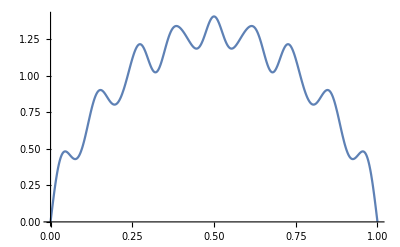

```mathematica
Plot[ϕn[0][b],{b,0,1}]
```

```mathematica
SessionTime[]/3600
```

1.048459978

```mathematica
Block[{i=50,j=50},NIntegrate[Boole[(y>x+λ||y<x-λ)]h2[i,j][x,y]+β^2 ϕ[i][x](2ϕ[j][x])/λ,{x,0,1},{y,0,1}]]
```

NIntegrate::inumr: The integrand Boole[y>1/100000+x∨y<-1/100000+x] h2(50,50)(x,y)+200000 ({0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,«8»,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}(x))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 1
0 | 1).

NIntegrate::inumr: The integrand Boole[y>1/100000+x∨y<-1/100000+x] h2(i,j)(x,y)+«1» has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 1
0 | 1).

NIntegrate[h2(i,j)(x,y) Boole[y>λ+x∨y<x-λ]+(β^2 ϕ(i)(x) (2 ϕ(j)(x)))/λ,{x,0,1},{y,0,1}]